```mathematica
ϵ0=8.85*^-12;h=6.626*^-34;ℏ=h/(2Pi);c=2.99792*^8;km=2Pi/(759*^-9);
m=171*1.67*^-27;Er=(ℏ*km)^2/(2m);α=179.3au;
au=1.6488*^-41;e=1.602*^-19;audipol=8.478*^-30;
```

```mathematica
Off[ClebschGordan::phy,ClebschGordan::tri,SixJSymbol::tri]
```

```mathematica
Er*2*ϵ0*c/α (*Intensity for 1 Er trap depth.*)
```

2.39509×10^6

```mathematica
ω3p={0,0,0};ω3p[[2]]=2Pi*c*17992.007*100-2Pi*c*17288.439*100;ω3p[[3]]=2Pi*c*19710.388*100-2Pi*c*17288.439*100;
```

```mathematica
λp={{1/(15406.253*100),1/(24326.601*100),1/(7200.663*100),1/(22520.281*100),1/(27022.941*100),1/(26516.981*100),1/((45121.37-17288.439)*100),1/((46877.10-17288.439)*100),1/((47885.81-17288.439)*100),1/((48519.71-17288.439)*100),1/((48943.42-17288.439)*100),1/((46444.96-17288.439)*100),1/((47400-17288.439)*100),1/((48357.6-17288.439)*100),1/((48838.1-17288.439)*100),1/((49161.1-17288.439)*100),1/((49399.1-17288.439)*100),1/((49576.4-17288.439)*100),1/((49712.1-17288.439)*100),1/((49818.2-17288.439)*100),1/((49902.8-17288.439)*100),1/((49971.3-17288.439)*100),1/((50027.7-17288.439)*100),1/((50074.4-17288.439)*100),1/((50113.7-17288.439)*100),1/((50147-17288.439)*100),1/((50175.6-17288.439)*100),1/((50200-17288.439)*100),1/((50221.5-17288.439)*100),1/((50240.1-17288.439)*100),1/((48762.5-17288.439)*100)},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}};
```

```mathematica
For[i=1,i≤31,i++,
λp[[2,i]]=1/(1/λp[[1,i]]+(17288.439*100)-17992.007*100);
λp[[3,i]]=1/(1/λp[[1,i]]+(17288.439*100)-19710.388*100);
]
```

```mathematica
λp//N
```

{{6.49087×10^-7,4.11073×10^-7,1.38876×10^-6,4.44044×10^-7,3.70056×10^-7,3.77117×10^-7,3.59287×10^-7,3.37967×10^-7,3.26825×10^-7,3.20192×10^-7,3.15906×10^-7,3.42976×10^-7,3.32098×10^-7,3.21863×10^-7,3.16961×10^-7,3.13749×10^-7,3.11423×10^-7,3.09713×10^-7,3.08417×10^-7,3.07411×10^-7,3.06613×10^-7,3.05971×10^-7,3.05444×10^-7,3.05009×10^-7,3.04643×10^-7,3.04335×10^-7,3.0407×10^-7,3.03845×10^-7,3.03646×10^-7,3.03475×10^-7,3.17722×10^-7},{6.80148×10^-7,4.23316×10^-7,1.53915×10^-6,4.58364×10^-7,3.79948×10^-7,3.87395×10^-7,3.68604×10^-7,3.46199×10^-7,3.34517×10^-7,3.27571×10^-7,3.23087×10^-7,3.51457×10^-7,3.40044×10^-7,3.2932×10^-7,3.2419×10^-7,3.20831×10^-7,3.18399×10^-7,3.16612×10^-7,3.15258×10^-7,3.14207×10^-7,3.13374×10^-7,3.12702×10^-7,3.12152×10^-7,3.11697×10^-7,3.11316×10^-7,3.10994×10^-7,3.10717×10^-7,3.10482×10^-7,3.10275×10^-7,3.10096×10^-7,3.24987×10^-7},{7.70161×10^-7,4.56524×10^-7,2.09261×10^-6,4.97554×10^-7,4.06488×10^-7,4.15023×10^-7,3.93531×10^-7,3.68098×10^-7,3.54919×10^-7,3.4711×10^-7,3.42079×10^-7,3.74048×10^-7,3.61146×10^-7,3.49074×10^-7,3.43316×10^-7,3.3955×10^-7,3.36828×10^-7,3.34829×10^-7,3.33314×10^-7,3.3214×10^-7,3.31209×10^-7,3.30459×10^-7,3.29845×10^-7,3.29337×10^-7,3.28912×10^-7,3.28552×10^-7,3.28243×10^-7,3.27981×10^-7,3.27749×10^-7,3.2755×10^-7,3.44209×10^-7}}

```mathematica
ωp=2Pi*c/λp;
```

```mathematica
ωp[[1,n]]-ωp[[3,n]]/.n->3
```

Part::pkspec1: The expression n cannot be used as a part specification.

4.5621×10^14

```mathematica
Akil={1/(14*^-9),1/(34*^-9),1/(376*^-9),1/(21*^-9),1/(38*^-9),1/(15*^-9),1/48*^-9,1/66*^-9,1/88*^-9,1/115*^-9,1/146*^-9,1/57*^-9,1/81*^-9,1/111*^-9,1/147*^-9,1/191*^-9,1/243*^-9,1/304*^-9,1/374*^-9,1/454*^-9,1/544*^-9,1/646*^-9,1/760*^-9,1/886*^-9,1/1026*^-9,1/1180*^-9,1/1348*^-9,1/1532*^-9,1/1730*^-9,1/1950*^-9,1/25*^-9};
```

```mathematica
Aki={{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},
{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}};
```

```mathematica
Jp={1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1};Lp={0,0,2,2,2,1,0,0,0,0,0,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2};
```

```mathematica
totbr[nt_]:=(Sqrt[(2*Jp[[nt]]+1)*(2*0+1)]*SixJSymbol[{Lp[[nt]],Jp[[nt]],1},{0,1,1}])^2*ωp[[0+1,nt]]^3+
(Sqrt[(2*Jp[[nt]]+1)*(2*1+1)]*SixJSymbol[{Lp[[nt]],Jp[[nt]],1},{1,1,1}])^2*ωp[[1+1,nt]]^3+
(Sqrt[(2*Jp[[nt]]+1)*(2*2+1)]*SixJSymbol[{Lp[[nt]],Jp[[nt]],1},{2,1,1}])^2*ωp[[2+1,nt]]^3;
```

```mathematica
br[jbr_,nbr_]:=(Sqrt[(2*Jp[[nbr]]+1)*(2*jbr+1)]*SixJSymbol[{Lp[[nbr]],Jp[[nbr]],1},{jbr,1,1}])^2*ωp[[jbr+1,nbr]]^3/totbr[nbr];
```

```mathematica
br[2,1]
```

0.453468

```mathematica
For[i=1,i≤31,i++,
(*Aki[[1,i]]=Akil[[i]]*br[0,i];*)
Aki[[1,i]]=Akil[[i]]*br[0,i];
Aki[[2,i]]=Akil[[i]]*br[1,i];
Aki[[3,i]]=Akil[[i]]*br[2,i];
]
```

```mathematica
RedMatL[na_,j3p_]:=Sqrt[(2*Lp[[na]]+1)*3*ϵ0*h*c^3/2/(ωp[[2,na]]^3)*Akil[[na]]];
```

```mathematica
RedMat[na_,j3p_]:=Sqrt[Aki[[j3p+1,na]]*(2*Jp[[na]]+1)*3*ϵ0*h*c^3/2/ωp[[j3p+1,na]]^3];
```

```mathematica
RedMat[1,2]/audipol
```

4.67974

```mathematica
Clear[Γ3P0,Int];c=2.99792*^8;ϵ0=8.85*^-12;h=6.626*^-34;ℏ=h/(2Pi);
RedMatFfk[fpb_,jpb_,lpb_,fb_,jb_,lb_,nb_]:=(-1)^(jpb+1/2+fb+1)*Sqrt[(2*fpb+1)*(2*fb+1)]*SixJSymbol[{jpb,fpb,1/2},{fb,jb,1}]*RedMat[nb,jpb];
RedMatFki[fpb_,jpb_,lpb_,npb_,fb_,jb_,lb_]:=(-1)^(jpb+1/2+fb+1)*Sqrt[(2*fpb+1)*(2*fb+1)]*SixJSymbol[{jpb,fpb,1/2},{fb,jb,1}]*RedMat[npb,jb];
MEfk[fpa_,mfpa_,jpa_,lpa_,qy_,fa_,mfa_,ja_,la_,na_]:=(-1)^(fpa-mfpa)*ThreeJSymbol[{fpa,-mfpa},{1,qy},{fa,mfa}]*RedMatFfk[fpa,jpa,lpa,fa,ja,la,na];
MEki[fpa_,mfpa_,jpa_,lpa_,npa_,qy_,fa_,mfa_,ja_,la_]:=(-1)^(fpa-mfpa)*ThreeJSymbol[{fpa,-mfpa},{1,qy},{fa,mfa}]*RedMatFki[fpa,jpa,lpa,npa,fa,ja,la];
Da[ω_,qx_,ffin_,mffin_,jfin_,lfin_]:=Sum[Sum[Sum[MEfk[ffin,mffin,jfin,lfin,qx,fk,mfk,Jp[[nk]],Lp[[nk]],nk]*MEki[fk,mfk,Jp[[nk]],Lp[[nk]],nk,0,1/2,1/2,0,1]/(ωp[[1,nk]]-ω)+MEfk[ffin,mffin,jfin,lfin,0,fk,mfk,Jp[[nk]],Lp[[nk]],nk]*MEki[fk,mfk,Jp[[nk]],Lp[[nk]],nk,qx,1/2,1/2,0,1]/(ωp[[1,nk]]+(ω-ω3p[[jfin+1]])),
{mfk,-fk,fk,1}],
{fk,Abs[1/2-Jp[[nk]]],1/2+Jp[[nk]],1}],
{nk,1,31,1}];
Γ3P0[ω_,Int_,ffin_,mffin_,jfin_,lfin_]:=Int*(ω-ω3p[[jfin+1]])^3/((4Pi*ϵ0)^2*c^4*ℏ^3)*8Pi/3*Sum[Da[ω,q,ffin,mffin,jfin,lfin]^2,{q,-1,1,1}];
```

```mathematica
Γ3P0[2Pi*c/(759*^-9),Er/α*2*ϵ0*c,5/2,3/2,2,1]*10^4
```

1.50463

```mathematica
Dapol[ω_,qx_,ffin_,mffin_,jfin_,lfin_,pol_]:=Sum[Sum[Sum[MEfk[ffin,mffin,jfin,lfin,qx,fk,mfk,Jp[[nk]],Lp[[nk]],nk]*MEki[fk,mfk,Jp[[nk]],Lp[[nk]],nk,pol,1/2,1/2,0,1]/(ωp[[1,nk]]-ω)+MEfk[ffin,mffin,jfin,lfin,pol,fk,mfk,Jp[[nk]],Lp[[nk]],nk]*MEki[fk,mfk,Jp[[nk]],Lp[[nk]],nk,qx,1/2,1/2,0,1]/(ωp[[1,nk]]+(ω-ω3p[[jfin+1]])),
{mfk,-fk,fk,1}],
{fk,Abs[1/2-Jp[[nk]]],1/2+Jp[[nk]],1}],
{nk,1,6,1}];
Γ3P0pol[ω_,Int_,ffin_,mffin_,jfin_,lfin_,pol_]:=Int*(ω-ω3p[[jfin+1]])^3/((4Pi*ϵ0)^2*c^4*ℏ^3)*8Pi/3*Sum[Dapol[ω,q,ffin,mffin,jfin,lfin,pol]^2,{q,-1,1,1}];
```

```mathematica
Γ3P0pol[2Pi*c/(556*^-9),1*^7,5/2,1/2,2,1,-1]*10^4
```

1.50329

```mathematica
Γ3P03P1[ω_]=Sum[Sum[Γ3P0[ω,1*^7,f,mf,1,1]*10^4,{mf,-1/2,f,1}],{f,1/2,3/2,1}];
```

```mathematica
Γ3P03P1[2Pi*c/(556*^-9)]
```

20.0708

```mathematica
16.8*^6*h/(250au/(2*ϵ0*c))/10^7
```

1433.

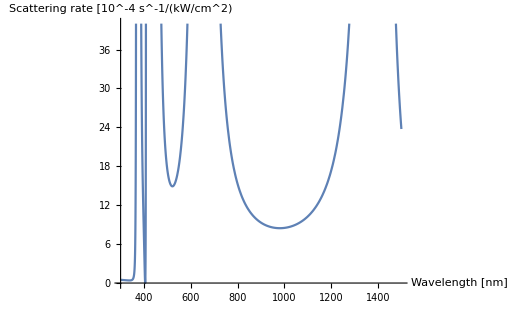

```mathematica
Plot[Γ3P03P1[2Pi*c/λ*1*^9],{λ,300,1500},PlotRange->{0,40},AxesLabel->{"Wavelength [nm]","Scattering rate [10^-4 s^-1/(kW/cm^2)"}]
```

```mathematica
Da[km*c,0,1/2,1/2,0,1]
```

-2.16378×10^-73

```mathematica
int=2*.64/(Pi*.05*^-3*1.55*^-3)
```

5.25725×10^6

```mathematica
ℏ*α
```

3.1176×10^-73

```mathematica
Γ3P03P2[ω_]=Sum[Sum[Γ3P0[ω,10*^7,f,mf,2,1]*10^4,{mf,-1/2,f,1}],{f,1/2,5/2,1}];
```

```mathematica
Γ3P03P2[2Pi*c/(556*^-9)]
```

250.548

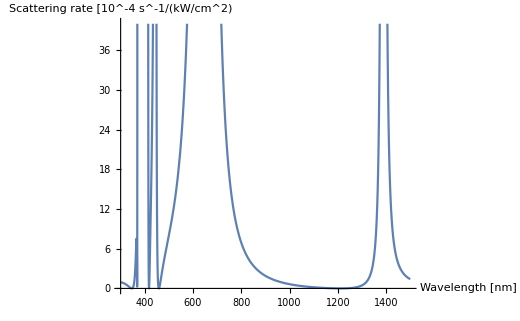

```mathematica
Plot[Γ3P03P2[2Pi*c/λ*1*^9],{λ,300,1500},PlotRange->{0,40},AxesLabel->{"Wavelength [nm]","Scattering rate [10^-4 s^-1/(kW/cm^2)"}]
```